## Code for generating the metric

Code I wrote for generating the metric for a Schwarzschild black hole in “Cartesian” coordinates,

```mathematica
coords={t,x,y,z};
sq[v_]:=v.v;
m=1;
metric=-(1-m/Sqrt[x^2+y^2+z^2])Dt[t]^2+(1-m/Sqrt[x^2+y^2+z^2])^(-1)((2 x Dt[x]+2 y Dt[y]+2 z Dt[z])/(2 √(x^2+y^2+z^2)))^2+sq[{Dt[x], Dt[y], Dt[z]} - {x, y, z}.{Dt[x], Dt[y], Dt[z]}/Sqrt[x^2 + y^2 + z^2]^2 {x, y, z}]//FullSimplify;
gfunc[list_]:=Times@@({Dt[t],Dt[x],Dt[y],Dt[z]}^(list-1));
subst=Flatten[MapIndexed[(If[gfunc[#2]=!=1,gfunc[#2],foo]->#1)&,FullSimplify[CoefficientList[metric,{Dt[t],Dt[x],Dt[y],Dt[z]}]],{4}]];

Print["Finding metric"];
metricmatrix=MapIndexed[If[#2[[1]]==#2[[2]],#1,#1/2]&,FullSimplify[Outer[Times,{Dt[t],Dt[x],Dt[y],Dt[z]},{Dt[t],Dt[x],Dt[y],Dt[z]}]/.subst],{2}];
Print["Finding metric inverse"];
metricmatrixUp=FullSimplify[Inverse[metricmatrix]];

g[μ_,ν_]:=metricmatrix[[μ,ν]];
gcomma[μ_,ν_,κ_]:=D[g[μ,ν],coords[[κ]]];
gUp[μ_,ν_]:=metricmatrixUp[[μ,ν]];
Γ[i_,j_,k_]:=1/2 Sum[gUp[i,l](gcomma[l,j,k]+gcomma[l,k,j]-gcomma[j,k,l]),{l,1,4}];
Print["Finding equations of motion"];
eqns=Table[Dt[Dt[coords[[i]]]]==-Sum[Dt[coords[[a]]]Dt[coords[[b]]]Γ[i,a,b]/.m->1,{a,1,4},{b,1,4}],{i,1,4}];
Print["Simplifying equations of motion"];
eqns=Simplify[eqns];
```

Finding metric

Finding metric inverse

Finding equations of motion

Simplifying equations of motion

```mathematica
metricmatrix//MatrixForm
```

(-1+1/(√(x^2+y^2+z^2)) | 0 | 0 | 0
0 | (x^2+((y^2+z^2) (-1+√(x^2+y^2+z^2)))/(√(x^2+y^2+z^2)))/(x^2+y^2+z^2-√(x^2+y^2+z^2)) | (x y)/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2))) | (x z)/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2)))
0 | (x y)/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2))) | 1+(y^2 (x^2+y^2+z^2+√(x^2+y^2+z^2)))/((-1+x^2+y^2+z^2) (x^2+y^2+z^2)^(3/2)) | (y z)/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2)))
0 | (x z)/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2))) | (y z)/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2))) | (x^2+y^2-√(x^2+y^2+z^2)+z^2 (1+1/(√(x^2+y^2+z^2))))/(x^2+y^2+z^2-√(x^2+y^2+z^2)))

```mathematica
metricmatrixUp//MatrixForm
```

(1/(-1+1/(√(x^2+y^2+z^2))) | 0 | 0 | 0
0 | 1-x^2/((x^2+y^2+z^2)^(3/2)) | -(x y)/((x^2+y^2+z^2)^(3/2)) | -(x z)/((x^2+y^2+z^2)^(3/2))
0 | -(x y)/((x^2+y^2+z^2)^(3/2)) | 1-y^2/((x^2+y^2+z^2)^(3/2)) | -(y z)/((x^2+y^2+z^2)^(3/2))
0 | -(x z)/((x^2+y^2+z^2)^(3/2)) | -(y z)/((x^2+y^2+z^2)^(3/2)) | 1-z^2/((x^2+y^2+z^2)^(3/2)))

## Code for plotting a geodesic to test things

```mathematica
positiveTprime=Simplify[dt0/.Solve[{dt0,dx0,dy0,dz0}.metricmatrix.{dt0,dx0,dy0,dz0}==0,dt0][[2]]];
eqns2=eqns/.{Dt[Dt[t]]->t''[τ],Dt[t]->t'[τ],t->t[τ],
Dt[Dt[x]]->x''[τ],Dt[x]->x'[τ],x->x[τ],
Dt[Dt[y]]->y''[τ],Dt[y]->y'[τ],y->y[τ],
Dt[Dt[z]]->z''[τ],Dt[z]->z'[τ],z->z[τ]};
plotGeodesic[x0v_,y0v_,dx0v_,dy0v_,options:OptionsPattern[]]:=Module[{tmp,incondsub,incond,nsoln},

incondsub={t0->0.,x0->x0v,y0->y0v,z0-> 0,dx0->dx0v,dy0->dy0v,dz0->0};
incond={t[0]==t0,x[0]==x0,y[0]==y0,z[0]==z0,x'[0]==dx0,y'[0]==dy0,z'[0]==dz0,t'[0]==Re@(positiveTprime/.{x->x0,t->t0,y->y0,z->z0})}/.incondsub;
nsoln=First@NDSolve[Join[eqns2,incond,{WhenEvent[x[τ]^2+y[τ]^2+z[τ]^2<2.0,"StopIntegration"]}],{t,x,y,z},{τ,0,100.}
];
min=(t/.nsoln)["Domain"][[1,1]];
max=(t/.nsoln)["Domain"][[1,2]];
ParametricPlot[{x[τ],y[τ]}/.nsoln,{τ,min,max},PlotRange->5,Evaluate[FilterRules[{options},Options[Plot]]]]
]
```

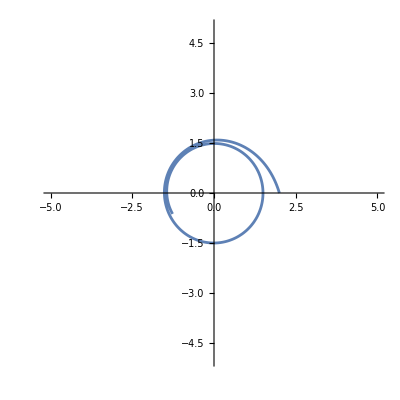

```mathematica
plotGeodesic[2,0,-0.3043,1]
```

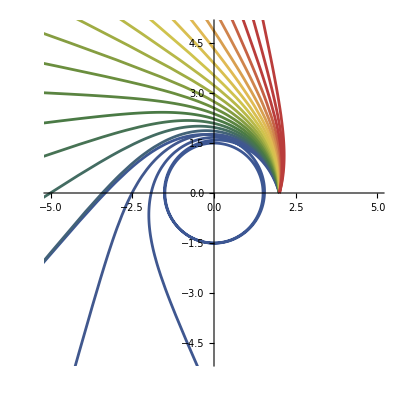

rays.png

```mathematica
SetDirectory[NotebookDirectory[]];
Export["rays.png",Echo@Show[Table[plotGeodesic[2,0,-0.30429+i,1,PlotStyle-> ColorData["DarkRainbow"][i/0.6]],{i,0,0.6,0.6/20}]]]
```

## Generating the C code for integration

```mathematica
FullForm[Element[#,Reals]&/@{x,y,z,t,dx,dy,dz,dt}]
```

List[Element[x,Reals],Element[y,Reals],Element[z,Reals],Element[t,Reals],Element[dx,Reals],Element[dy,Reals],Element[dz,Reals],Element[dt,Reals]]

```mathematica
equationsSimplified=FullSimplify[{ddt,ddx,ddy,ddz}/.Solve[eqns/.{Dt[Dt[t]]->ddt,Dt[t]->dt,t->t,
Dt[Dt[x]]->ddx,Dt[x]->dx,x->x,
Dt[Dt[y]]->ddy,Dt[y]->dy,y->y,
Dt[Dt[z]]->ddz,Dt[z]->dz,z->z},{ddt,ddx,ddy,ddz}][[1]],Assumptions->{Element[x,Reals],Element[y,Reals],Element[z,Reals],Element[t,Reals],Element[dx,Reals],Element[dy,Reals],Element[dz,Reals],Element[dt,Reals]}]
```

{-(dt (dx x+dy y+dz z))/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2))),(x (dx^2 x^2 √(x^2+y^2+z^2)+2 dx dz x z √(x^2+y^2+z^2)+dz^2 z^2 √(x^2+y^2+z^2)+2 dx dz x z (-2+3 x^2+3 y^2+3 z^2)-dz^2 (2 (-1+x^2+y^2) (x^2+y^2)+(x^2+y^2) z^2-z^4)+dt^2 (-1+x^2+y^2+z^2) (-x^2-y^2-z^2+√(x^2+y^2+z^2))+2 dy y (dx x+dz z) (-2+3 x^2+3 y^2+3 z^2+√(x^2+y^2+z^2))+dx^2 (2 (y^2+z^2)+(x^2+y^2+z^2) (x^2-2 (y^2+z^2)))+dy^2 (-2 x^4+y^4+2 z^2-2 z^4-x^2 (-2+y^2+4 z^2)+y^2 (-z^2+√(x^2+y^2+z^2)))))/(2 (-1+x^2+y^2+z^2) (x^2+y^2+z^2)^(5/2)),(y (dx^2 x^2 √(x^2+y^2+z^2)+2 dx dz x z √(x^2+y^2+z^2)+dz^2 z^2 √(x^2+y^2+z^2)+2 dx dz x z (-2+3 x^2+3 y^2+3 z^2)-dz^2 (2 (-1+x^2+y^2) (x^2+y^2)+(x^2+y^2) z^2-z^4)+dt^2 (-1+x^2+y^2+z^2) (-x^2-y^2-z^2+√(x^2+y^2+z^2))+2 dy y (dx x+dz z) (-2+3 x^2+3 y^2+3 z^2+√(x^2+y^2+z^2))+dx^2 (2 (y^2+z^2)+(x^2+y^2+z^2) (x^2-2 (y^2+z^2)))+dy^2 (-2 x^4+y^4+2 z^2-2 z^4-x^2 (-2+y^2+4 z^2)+y^2 (-z^2+√(x^2+y^2+z^2)))))/(2 (-1+x^2+y^2+z^2) (x^2+y^2+z^2)^(5/2)),(z (dx^2 x^2 √(x^2+y^2+z^2)+2 dx dz x z √(x^2+y^2+z^2)+dz^2 z^2 √(x^2+y^2+z^2)+2 dx dz x z (-2+3 x^2+3 y^2+3 z^2)-dz^2 (2 (-1+x^2+y^2) (x^2+y^2)+(x^2+y^2) z^2-z^4)+dt^2 (-1+x^2+y^2+z^2) (-x^2-y^2-z^2+√(x^2+y^2+z^2))+2 dy y (dx x+dz z) (-2+3 x^2+3 y^2+3 z^2+√(x^2+y^2+z^2))+dx^2 (2 (y^2+z^2)+(x^2+y^2+z^2) (x^2-2 (y^2+z^2)))+dy^2 (-2 x^4+y^4+2 z^2-2 z^4-x^2 (-2+y^2+4 z^2)+y^2 (-z^2+√(x^2+y^2+z^2)))))/(2 (-1+x^2+y^2+z^2) (x^2+y^2+z^2)^(5/2))}

```mathematica
StringRiffle[{"double ddt = "<>ToString[CForm[equationsSimplified[[1]]]]<>";",
"double ddx = "<>ToString[CForm[equationsSimplified[[2]]]]<>";",
"double ddy = "<>ToString[CForm[equationsSimplified[[3]]]]<>";",
"double ddz = "<>ToString[CForm[equationsSimplified[[4]]]]<>";"
},"\n\n"]
```

double ddt = -((dt*(dx*x + dy*y + dz*z))/((Power(x,2) + Power(y,2) + Power(z,2))*(-1 + Sqrt(Power(x,2) + Power(y,2) + Power(z,2)))));

double ddx = (x*(Power(dx,2)*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy*y*(dx*x + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dx,2)*(2*(Power(y,2) + Power(z,2)) + (Power(x,2) + Power(y,2) + Power(z,2))*(Power(x,2) - 2*(Power(y,2) + Power(z,2)))) + Power(dy,2)*(-2*Power(x,4) + Power(y,4) + 2*Power(z,2) - 2*Power(z,4) - Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2)) + Power(y,2)*(-Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5));

double ddy = (y*(Power(dx,2)*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy*y*(dx*x + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dx,2)*(2*(Power(y,2) + Power(z,2)) + (Power(x,2) + Power(y,2) + Power(z,2))*(Power(x,2) - 2*(Power(y,2) + Power(z,2)))) + Power(dy,2)*(-2*Power(x,4) + Power(y,4) + 2*Power(z,2) - 2*Power(z,4) - Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2)) + Power(y,2)*(-Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5));

double ddz = (z*(Power(dx,2)*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy*y*(dx*x + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dx,2)*(2*(Power(y,2) + Power(z,2)) + (Power(x,2) + Power(y,2) + Power(z,2))*(Power(x,2) - 2*(Power(y,2) + Power(z,2)))) + Power(dy,2)*(-2*Power(x,4) + Power(y,4) + 2*Power(z,2) - 2*Power(z,4) - Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2)) + Power(y,2)*(-Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5));

```mathematica
ToString[CForm[equationsSimplified]]
```

List(-((dt*(dx*x + dy*y + dz*z))/((Power(x,2) + Power(y,2) + Power(z,2))*(-1 + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))),(x*(Power(dx,2)*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy*y*(dx*x + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dx,2)*(2*(Power(y,2) + Power(z,2)) + (Power(x,2) + Power(y,2) + Power(z,2))*(Power(x,2) - 2*(Power(y,2) + Power(z,2)))) + Power(dy,2)*(-2*Power(x,4) + Power(y,4) + 2*Power(z,2) - 2*Power(z,4) - Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2)) + Power(y,2)*(-Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5)),(y*(Power(dx,2)*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy*y*(dx*x + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dx,2)*(2*(Power(y,2) + Power(z,2)) + (Power(x,2) + Power(y,2) + Power(z,2))*(Power(x,2) - 2*(Power(y,2) + Power(z,2)))) + Power(dy,2)*(-2*Power(x,4) + Power(y,4) + 2*Power(z,2) - 2*Power(z,4) - Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2)) + Power(y,2)*(-Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5)),(z*(Power(dx,2)*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dx*dz*x*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy*y*(dx*x + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dx,2)*(2*(Power(y,2) + Power(z,2)) + (Power(x,2) + Power(y,2) + Power(z,2))*(Power(x,2) - 2*(Power(y,2) + Power(z,2)))) + Power(dy,2)*(-2*Power(x,4) + Power(y,4) + 2*Power(z,2) - 2*Power(z,4) - Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2)) + Power(y,2)*(-Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5)))

NB: you can use code like this to generate simpler representations where multiplication is used instead of “power”.

```mathematica
parser=StringReplace[ToString[CForm[#]],Shortest["Power("~~x__~~",2)"]:>x<>"*"<>x]&;
```

## Delete:

```mathematica
ToString[CForm[#]]&/@(eqnsfinal/.{Dt[t]->dt,t->t,
Dt[x]->dx,x->x,
Dt[y]->dy,y->y,
Dt[z]->dz,z->z})
```

{Dt(dt) == -((dt*(dx*x + dy*y + dz*z))/((Power(x,2) + Power(y,2) + Power(z,2))*(-1 + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))),Dt(dx) == (x*(Power(dy,2)*Power(y,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dy*dz*y*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dy*dz*y*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dx*x*(dy*y + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) - Power(dy,2)*(2*Power(x,4) - Power(y,4) + (-2 + Power(y,2))*Power(z,2) + 2*Power(z,4) + Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2))) + Power(dx,2)*(Power(x,4) - 2*(-1 + Power(y,2) + Power(z,2))*(Power(y,2) + Power(z,2)) + Power(x,2)*(-Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5)),Dt(dy) == (y*(Power(dy,2)*Power(y,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dy*dz*y*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dy*dz*y*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dx*x*(dy*y + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) - Power(dy,2)*(2*Power(x,4) - Power(y,4) + (-2 + Power(y,2))*Power(z,2) + 2*Power(z,4) + Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2))) + Power(dx,2)*(Power(x,4) - 2*(-1 + Power(y,2) + Power(z,2))*(Power(y,2) + Power(z,2)) + Power(x,2)*(-Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5)),Dt(dz) == (z*(Power(dy,2)*Power(y,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dy*dz*y*z*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(dz,2)*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + 2*dy*dz*y*z*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2)) - Power(dz,2)*(2*(-1 + Power(x,2) + Power(y,2))*(Power(x,2) + Power(y,2)) + (Power(x,2) + Power(y,2))*Power(z,2) - Power(z,4)) + Power(dt,2)*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*(-Power(x,2) - Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dx*x*(dy*y + dz*z)*(-2 + 3*Power(x,2) + 3*Power(y,2) + 3*Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) - Power(dy,2)*(2*Power(x,4) - Power(y,4) + (-2 + Power(y,2))*Power(z,2) + 2*Power(z,4) + Power(x,2)*(-2 + Power(y,2) + 4*Power(z,2))) + Power(dx,2)*(Power(x,4) - 2*(-1 + Power(y,2) + Power(z,2))*(Power(y,2) + Power(z,2)) + Power(x,2)*(-Power(y,2) - Power(z,2) + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))/(2.*(-1 + Power(x,2) + Power(y,2) + Power(z,2))*Power(Power(x,2) + Power(y,2) + Power(z,2),2.5))}

```mathematica
f[2,2,2,-0.0,1,-1]
```

{229.247,24.1191,138.349,-90.1108,2.34316,0.225838,1.37835,-0.926671}

```mathematica
ParametricPlot3D[{x[τ],y[τ],z[τ]}/.nsoln,{τ,0,10},PlotRange->3]
```

```mathematica
x/.First@NDSolve[{x'[t]==-1/x[t],x[0]==1},x,{t,0,0.24}]
```

InterpolatingFunction[{{0., 0.24}}, <>]

```mathematica
%551["Domain"]=={{0.,0.24}}
```

True

```mathematica
incond
```

```mathematica
gUP
```

{t[0]==0.,x[0]==2.,y[0]==0.,z[0]==0.,x'[0]==0.,y'[0]==1.,z'[0]==0.,t'[0]==1.41421}

```mathematica
positiveTprime=Simplify[dt0/.Solve[{dt0,dx0,dy0,dz0}.metricmatrix.{dt0,dx0,dy0,dz0}==0,dt0][[2]]];
```

```mathematica
tmp
```

```mathematica
tmp=1/(√(1-1/(√(x^2+y^2+z^2))))(√(((2 dx0 dz0 x z (-1+√(x^2+y^2+z^2))+2 dy0 y (dx0 x+dz0 z) (-1+√(x^2+y^2+z^2))+dy0^2 (x^4+z^2+(y^2+z^2)^2-2 x^2 √(x^2+y^2+z^2)-y^2 √(x^2+y^2+z^2)-2 z^2 √(x^2+y^2+z^2)+x^2 (1+2 y^2+2 z^2))+dz0^2 (x^4+y^4+z^4-z^2 √(x^2+y^2+z^2)+y^2 (1+2 z^2-2 √(x^2+y^2+z^2))+x^2 (1+2 y^2+2 z^2-2 √(x^2+y^2+z^2)))+dx0^2 (x^4+(y^2+z^2) (1+y^2+z^2-2 √(x^2+y^2+z^2))+x^2 (2 y^2+2 z^2-√(x^2+y^2+z^2))))/((x^2+y^2+z^2) (1+x^2+y^2+z^2-2 √(x^2+y^2+z^2))))));
```

```mathematica
FullSimplif]
```

1/(√(-1+1/(√(x^2+y^2+z^2))))(√(-((2 dx0 dz0 x z (-1+√(x^2+y^2+z^2))+2 dy0 y (dx0 x+dz0 z) (-1+√(x^2+y^2+z^2))+dy0^2 (x^4+z^2+(y^2+z^2)^2-2 x^2 √(x^2+y^2+z^2)-y^2 √(x^2+y^2+z^2)-2 z^2 √(x^2+y^2+z^2)+x^2 (1+2 y^2+2 z^2))+dz0^2 (x^4+y^4+z^4-z^2 √(x^2+y^2+z^2)+y^2 (1+2 z^2-2 √(x^2+y^2+z^2))+x^2 (1+2 y^2+2 z^2-2 √(x^2+y^2+z^2)))+dx0^2 (x^4+(y^2+z^2) (1+y^2+z^2-2 √(x^2+y^2+z^2))+x^2 (2 y^2+2 z^2-√(x^2+y^2+z^2))))/((x^2+y^2+z^2) (1+x^2+y^2+z^2-2 √(x^2+y^2+z^2))))))

```mathematica
tmp/.{x->4.0,y->0.0,z->0.0,dx0->0.3,dy0->0.1,dz0->0.6}
```

0.80829+0. ⅈ

```mathematica
tmp=%158;
```

```mathematica
ToString[CForm[tmp]]
```

Sqrt((2*dx0*dz0*x*z*(-1 + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy0*y*(dx0*x + dz0*z)*(-1 + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dy0,2)*(Power(x,4) + Power(z,2) + Power(Power(y,2) + Power(z,2),2) - 2*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) - Power(y,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) - 2*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(x,2)*(1 + 2*Power(y,2) + 2*Power(z,2))) + Power(dz0,2)*(Power(x,4) + Power(y,4) + Power(z,4) - Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(y,2)*(1 + 2*Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(x,2)*(1 + 2*Power(y,2) + 2*Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)))) + Power(dx0,2)*(Power(x,4) + (Power(y,2) + Power(z,2))*(1 + Power(y,2) + Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(x,2)*(2*Power(y,2) + 2*Power(z,2) - Sqrt(Power(x,2) + Power(y,2) + Power(z,2)))))/((Power(x,2) + Power(y,2) + Power(z,2))*(1 + Power(x,2) + Power(y,2) + Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)))))/Sqrt(1 - 1/Sqrt(Power(x,2) + Power(y,2) + Power(z,2)))

```mathematica
ToString[CForm[#]]&/@(tmp/.{Dt[t]->dt,t->t,
dx0->dx,x->x,
dy0->dy,y->y,
dz0->dz,z->z})
```

1/Sqrt(-1 + 1/Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) Sqrt(-((2*dx*dz*x*z*(-1 + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + 2*dy*y*(dx*x + dz*z)*(-1 + Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(dy,2)*(Power(x,4) + Power(z,2) + Power(Power(y,2) + Power(z,2),2) - 2*Power(x,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) - Power(y,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) - 2*Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(x,2)*(1 + 2*Power(y,2) + 2*Power(z,2))) + Power(dz,2)*(Power(x,4) + Power(y,4) + Power(z,4) - Power(z,2)*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)) + Power(y,2)*(1 + 2*Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(x,2)*(1 + 2*Power(y,2) + 2*Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2)))) + Power(dx,2)*(Power(x,4) + (Power(y,2) + Power(z,2))*(1 + Power(y,2) + Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2))) + Power(x,2)*(2*Power(y,2) + 2*Power(z,2) - Sqrt(Power(x,2) + Power(y,2) + Power(z,2)))))/((Power(x,2) + Power(y,2) + Power(z,2))*(1 + Power(x,2) + Power(y,2) + Power(z,2) - 2*Sqrt(Power(x,2) + Power(y,2) + Power(z,2))))))

```mathematica
positiveTprime
```

1/(√(-1+1/(√(x^2+y^2+z^2))))(√(-((2 dx0 dz0 x z (-1+√(x^2+y^2+z^2))+2 dy0 y (dx0 x+dz0 z) (-1+√(x^2+y^2+z^2))+dz0^2 (x^4+y^4+z^4-z^2 √(x^2+y^2+z^2)+y^2 (1+2 z^2-2 √(x^2+y^2+z^2))+x^2 (1+2 y^2+2 z^2-2 √(x^2+y^2+z^2)))+dx0^2 (x^4+(y^2+z^2) (1+y^2+z^2-2 √(x^2+y^2+z^2))+x^2 (2 y^2+2 z^2-√(x^2+y^2+z^2)))+dy0^2 (x^4+y^4+z^2 (1+z^2-2 √(x^2+y^2+z^2))+x^2 (1+2 y^2+2 z^2-2 √(x^2+y^2+z^2))-y^2 (-2 z^2+√(x^2+y^2+z^2))))/(√(x^2+y^2+z^2) (x^2+y^2+z^2-√(x^2+y^2+z^2)) (-1+√(x^2+y^2+z^2))))))

```mathematica
NDSolve[eqns
```

```mathematica
coords
```

```mathematica
Dt[x[a]]
```

Dt[a] x'[a]

{Dt[Dt[t]]==(Dt[t] (x Dt[x]+y Dt[y]+z Dt[z]))/((x^2+y^2+z^2) (-1+√(x^2+y^2+z^2))),Dt[Dt[x]]==(x ((x^2+y^2+z^2) (-1-3 z^2+3 √(x^2+y^2+z^2)+z^2 √(x^2+y^2+z^2)+x^2 (-3+√(x^2+y^2+z^2))+y^2 (-3+√(x^2+y^2+z^2))) Dt[t]^2+(x^2 (y^2+z^2) (-3+√(x^2+y^2+z^2))-x^4 (-1+√(x^2+y^2+z^2))+2 (y^2+z^2) (√(x^2+y^2+z^2)+y^2 (-2+√(x^2+y^2+z^2))+z^2 (-2+√(x^2+y^2+z^2)))) Dt[x]^2-4 x^4 Dt[y]^2-3 x^2 y^2 Dt[y]^2+y^4 Dt[y]^2-8 x^2 z^2 Dt[y]^2-3 y^2 z^2 Dt[y]^2-4 z^4 Dt[y]^2+2 x^2 √(x^2+y^2+z^2) Dt[y]^2+2 x^4 √(x^2+y^2+z^2) Dt[y]^2+x^2 y^2 √(x^2+y^2+z^2) Dt[y]^2-y^4 √(x^2+y^2+z^2) Dt[y]^2+2 z^2 √(x^2+y^2+z^2) Dt[y]^2+4 x^2 z^2 √(x^2+y^2+z^2) Dt[y]^2+y^2 z^2 √(x^2+y^2+z^2) Dt[y]^2+2 z^4 √(x^2+y^2+z^2) Dt[y]^2+10 x^2 y z Dt[y] Dt[z]+10 y^3 z Dt[y] Dt[z]+10 y z^3 Dt[y] Dt[z]-4 y z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 x^2 y z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 y^3 z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 y z^3 √(x^2+y^2+z^2) Dt[y] Dt[z]-4 x^4 Dt[z]^2-8 x^2 y^2 Dt[z]^2-4 y^4 Dt[z]^2-3 x^2 z^2 Dt[z]^2-3 y^2 z^2 Dt[z]^2+z^4 Dt[z]^2+2 x^2 √(x^2+y^2+z^2) Dt[z]^2+2 x^4 √(x^2+y^2+z^2) Dt[z]^2+2 y^2 √(x^2+y^2+z^2) Dt[z]^2+4 x^2 y^2 √(x^2+y^2+z^2) Dt[z]^2+2 y^4 √(x^2+y^2+z^2) Dt[z]^2+x^2 z^2 √(x^2+y^2+z^2) Dt[z]^2+y^2 z^2 √(x^2+y^2+z^2) Dt[z]^2-z^4 √(x^2+y^2+z^2) Dt[z]^2-2 x (-5 z^2+2 √(x^2+y^2+z^2)+3 z^2 √(x^2+y^2+z^2)+x^2 (-5+3 √(x^2+y^2+z^2))+y^2 (-5+3 √(x^2+y^2+z^2))) Dt[x] (y Dt[y]+z Dt[z])))/(2 (x^2+y^2+z^2)^3 (-1+√(x^2+y^2+z^2))^2),Dt[Dt[y]]==(y ((x^2+y^2+z^2) (-1-3 z^2+3 √(x^2+y^2+z^2)+z^2 √(x^2+y^2+z^2)+x^2 (-3+√(x^2+y^2+z^2))+y^2 (-3+√(x^2+y^2+z^2))) Dt[t]^2+(x^2 (y^2+z^2) (-3+√(x^2+y^2+z^2))-x^4 (-1+√(x^2+y^2+z^2))+2 (y^2+z^2) (√(x^2+y^2+z^2)+y^2 (-2+√(x^2+y^2+z^2))+z^2 (-2+√(x^2+y^2+z^2)))) Dt[x]^2-4 x^4 Dt[y]^2-3 x^2 y^2 Dt[y]^2+y^4 Dt[y]^2-8 x^2 z^2 Dt[y]^2-3 y^2 z^2 Dt[y]^2-4 z^4 Dt[y]^2+2 x^2 √(x^2+y^2+z^2) Dt[y]^2+2 x^4 √(x^2+y^2+z^2) Dt[y]^2+x^2 y^2 √(x^2+y^2+z^2) Dt[y]^2-y^4 √(x^2+y^2+z^2) Dt[y]^2+2 z^2 √(x^2+y^2+z^2) Dt[y]^2+4 x^2 z^2 √(x^2+y^2+z^2) Dt[y]^2+y^2 z^2 √(x^2+y^2+z^2) Dt[y]^2+2 z^4 √(x^2+y^2+z^2) Dt[y]^2+10 x^2 y z Dt[y] Dt[z]+10 y^3 z Dt[y] Dt[z]+10 y z^3 Dt[y] Dt[z]-4 y z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 x^2 y z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 y^3 z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 y z^3 √(x^2+y^2+z^2) Dt[y] Dt[z]-4 x^4 Dt[z]^2-8 x^2 y^2 Dt[z]^2-4 y^4 Dt[z]^2-3 x^2 z^2 Dt[z]^2-3 y^2 z^2 Dt[z]^2+z^4 Dt[z]^2+2 x^2 √(x^2+y^2+z^2) Dt[z]^2+2 x^4 √(x^2+y^2+z^2) Dt[z]^2+2 y^2 √(x^2+y^2+z^2) Dt[z]^2+4 x^2 y^2 √(x^2+y^2+z^2) Dt[z]^2+2 y^4 √(x^2+y^2+z^2) Dt[z]^2+x^2 z^2 √(x^2+y^2+z^2) Dt[z]^2+y^2 z^2 √(x^2+y^2+z^2) Dt[z]^2-z^4 √(x^2+y^2+z^2) Dt[z]^2-2 x (-5 z^2+2 √(x^2+y^2+z^2)+3 z^2 √(x^2+y^2+z^2)+x^2 (-5+3 √(x^2+y^2+z^2))+y^2 (-5+3 √(x^2+y^2+z^2))) Dt[x] (y Dt[y]+z Dt[z])))/(2 (x^2+y^2+z^2)^3 (-1+√(x^2+y^2+z^2))^2),Dt[Dt[z]]==(z ((x^2+y^2+z^2) (-1-3 z^2+3 √(x^2+y^2+z^2)+z^2 √(x^2+y^2+z^2)+x^2 (-3+√(x^2+y^2+z^2))+y^2 (-3+√(x^2+y^2+z^2))) Dt[t]^2+(x^2 (y^2+z^2) (-3+√(x^2+y^2+z^2))-x^4 (-1+√(x^2+y^2+z^2))+2 (y^2+z^2) (√(x^2+y^2+z^2)+y^2 (-2+√(x^2+y^2+z^2))+z^2 (-2+√(x^2+y^2+z^2)))) Dt[x]^2-4 x^4 Dt[y]^2-3 x^2 y^2 Dt[y]^2+y^4 Dt[y]^2-8 x^2 z^2 Dt[y]^2-3 y^2 z^2 Dt[y]^2-4 z^4 Dt[y]^2+2 x^2 √(x^2+y^2+z^2) Dt[y]^2+2 x^4 √(x^2+y^2+z^2) Dt[y]^2+x^2 y^2 √(x^2+y^2+z^2) Dt[y]^2-y^4 √(x^2+y^2+z^2) Dt[y]^2+2 z^2 √(x^2+y^2+z^2) Dt[y]^2+4 x^2 z^2 √(x^2+y^2+z^2) Dt[y]^2+y^2 z^2 √(x^2+y^2+z^2) Dt[y]^2+2 z^4 √(x^2+y^2+z^2) Dt[y]^2+10 x^2 y z Dt[y] Dt[z]+10 y^3 z Dt[y] Dt[z]+10 y z^3 Dt[y] Dt[z]-4 y z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 x^2 y z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 y^3 z √(x^2+y^2+z^2) Dt[y] Dt[z]-6 y z^3 √(x^2+y^2+z^2) Dt[y] Dt[z]-4 x^4 Dt[z]^2-8 x^2 y^2 Dt[z]^2-4 y^4 Dt[z]^2-3 x^2 z^2 Dt[z]^2-3 y^2 z^2 Dt[z]^2+z^4 Dt[z]^2+2 x^2 √(x^2+y^2+z^2) Dt[z]^2+2 x^4 √(x^2+y^2+z^2) Dt[z]^2+2 y^2 √(x^2+y^2+z^2) Dt[z]^2+4 x^2 y^2 √(x^2+y^2+z^2) Dt[z]^2+2 y^4 √(x^2+y^2+z^2) Dt[z]^2+x^2 z^2 √(x^2+y^2+z^2) Dt[z]^2+y^2 z^2 √(x^2+y^2+z^2) Dt[z]^2-z^4 √(x^2+y^2+z^2) Dt[z]^2-2 x (-5 z^2+2 √(x^2+y^2+z^2)+3 z^2 √(x^2+y^2+z^2)+x^2 (-5+3 √(x^2+y^2+z^2))+y^2 (-5+3 √(x^2+y^2+z^2))) Dt[x] (y Dt[y]+z Dt[z])))/(2 (x^2+y^2+z^2)^3 (-1+√(x^2+y^2+z^2))^2)}

```mathematica
Γ[3,3,1]
```

0

```mathematica
Γ[1,1,4]
```

0

```mathematica
metricmatrix//MatrixForm
```

(-1+m/(√(x^2+y^2+z^2)) | 0 | 0 | 0
0 | (-m (y^2+z^2)+(x^2+y^2+z^2)^(3/2))/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))) | (m x y)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))) | (m x z)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2)))
0 | (m x y)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))) | 1+(m y^2)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))) | (m y z)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2)))
0 | (m x z)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))) | (m y z)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))) | (-m (x^2+y^2)+(x^2+y^2+z^2)^(3/2))/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))))

```mathematica
FullSimplify[Inverse[metricmatrix]]//MatrixForm
```

(1/(-1+m/(√(x^2+y^2+z^2))) | 0 | 0 | 0
0 | 1-(m x^2)/((x^2+y^2+z^2)^(3/2)) | -(m x y)/((x^2+y^2+z^2)^(3/2)) | -(m x z)/((x^2+y^2+z^2)^(3/2))
0 | -(m x y)/((x^2+y^2+z^2)^(3/2)) | 1-(m y^2)/((x^2+y^2+z^2)^(3/2)) | -(m y z)/((x^2+y^2+z^2)^(3/2))
0 | -(m x z)/((x^2+y^2+z^2)^(3/2)) | -(m y z)/((x^2+y^2+z^2)^(3/2)) | 1-(m z^2)/((x^2+y^2+z^2)^(3/2)))

```mathematica
Times@@{a,b,c,d}
```

a b c d

```mathematica
{a,b,c,d}^{1,2,3,4}
```

{a,b^2,c^3,d^4}

```mathematica
g[{1,2,3,1}]
```

Dt[x] Dt[y]^2

```mathematica
(#1->g[#2])&
```

{foo→0,Dt[z]→0,Dt[z]^2→(-m (x^2+y^2)+(x^2+y^2+z^2)^(3/2))/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))),Dt[y]→0,Dt[y] Dt[z]→(2 m y z)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))),Dt[y] Dt[z]^2→0,Dt[y]^2→1+(m y^2)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))),Dt[y]^2 Dt[z]→0,Dt[y]^2 Dt[z]^2→0,Dt[x]→0,Dt[x] Dt[z]→(2 m x z)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))),Dt[x] Dt[z]^2→0,Dt[x] Dt[y]→(2 m x y)/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))),Dt[x] Dt[y] Dt[z]→0,Dt[x] Dt[y] Dt[z]^2→0,Dt[x] Dt[y]^2→0,Dt[x] Dt[y]^2 Dt[z]→0,Dt[x] Dt[y]^2 Dt[z]^2→0,Dt[x]^2→(-m (y^2+z^2)+(x^2+y^2+z^2)^(3/2))/((x^2+y^2+z^2) (-m+√(x^2+y^2+z^2))),Dt[x]^2 Dt[z]→0,Dt[x]^2 Dt[z]^2→0,Dt[x]^2 Dt[y]→0,Dt[x]^2 Dt[y] Dt[z]→0,Dt[x]^2 Dt[y] Dt[z]^2→0,Dt[x]^2 Dt[y]^2→0,Dt[x]^2 Dt[y]^2 Dt[z]→0,Dt[x]^2 Dt[y]^2 Dt[z]^2→0,Dt[t]→0,Dt[t] Dt[z]→0,Dt[t] Dt[z]^2→0,Dt[t] Dt[y]→0,Dt[t] Dt[y] Dt[z]→0,Dt[t] Dt[y] Dt[z]^2→0,Dt[t] Dt[y]^2→0,Dt[t] Dt[y]^2 Dt[z]→0,Dt[t] Dt[y]^2 Dt[z]^2→0,Dt[t] Dt[x]→0,Dt[t] Dt[x] Dt[z]→0,Dt[t] Dt[x] Dt[z]^2→0,Dt[t] Dt[x] Dt[y]→0,Dt[t] Dt[x] Dt[y] Dt[z]→0,Dt[t] Dt[x] Dt[y] Dt[z]^2→0,Dt[t] Dt[x] Dt[y]^2→0,Dt[t] Dt[x] Dt[y]^2 Dt[z]→0,Dt[t] Dt[x] Dt[y]^2 Dt[z]^2→0,Dt[t] Dt[x]^2→0,Dt[t] Dt[x]^2 Dt[z]→0,Dt[t] Dt[x]^2 Dt[z]^2→0,Dt[t] Dt[x]^2 Dt[y]→0,Dt[t] Dt[x]^2 Dt[y] Dt[z]→0,Dt[t] Dt[x]^2 Dt[y] Dt[z]^2→0,Dt[t] Dt[x]^2 Dt[y]^2→0,Dt[t] Dt[x]^2 Dt[y]^2 Dt[z]→0,Dt[t] Dt[x]^2 Dt[y]^2 Dt[z]^2→0,Dt[t]^2→-1+m/(√(x^2+y^2+z^2)),Dt[t]^2 Dt[z]→0,Dt[t]^2 Dt[z]^2→0,Dt[t]^2 Dt[y]→0,Dt[t]^2 Dt[y] Dt[z]→0,Dt[t]^2 Dt[y] Dt[z]^2→0,Dt[t]^2 Dt[y]^2→0,Dt[t]^2 Dt[y]^2 Dt[z]→0,Dt[t]^2 Dt[y]^2 Dt[z]^2→0,Dt[t]^2 Dt[x]→0,Dt[t]^2 Dt[x] Dt[z]→0,Dt[t]^2 Dt[x] Dt[z]^2→0,Dt[t]^2 Dt[x] Dt[y]→0,Dt[t]^2 Dt[x] Dt[y] Dt[z]→0,Dt[t]^2 Dt[x] Dt[y] Dt[z]^2→0,Dt[t]^2 Dt[x] Dt[y]^2→0,Dt[t]^2 Dt[x] Dt[y]^2 Dt[z]→0,Dt[t]^2 Dt[x] Dt[y]^2 Dt[z]^2→0,Dt[t]^2 Dt[x]^2→0,Dt[t]^2 Dt[x]^2 Dt[z]→0,Dt[t]^2 Dt[x]^2 Dt[z]^2→0,Dt[t]^2 Dt[x]^2 Dt[y]→0,Dt[t]^2 Dt[x]^2 Dt[y] Dt[z]→0,Dt[t]^2 Dt[x]^2 Dt[y] Dt[z]^2→0,Dt[t]^2 Dt[x]^2 Dt[y]^2→0,Dt[t]^2 Dt[x]^2 Dt[y]^2 Dt[z]→0,Dt[t]^2 Dt[x]^2 Dt[y]^2 Dt[z]^2→0}

```mathematica
CoefficientList
```

```mathematica
subs={r->Sqrt[x^2+y^2+z^2],Cos[θ]->z/Sqrt[x^2+y^2+z^2],Sin[θ]->Sqrt[x^2+y^2]/Sqrt[x^2+y^2+z^2],Sin[ϕ]->y/Sqrt[x^2+y^2],Cos[ϕ]->x/Sqrt[x^2+y^2]};
```

```mathematica
FullSimplify[Solve[(Dt[Sin[θ]]/.subs)==Dt[Sin[θ]/.subs],Dt[θ]]]
```

{{Dt[θ]→(x z Dt[x]+y z Dt[y]-(x^2+y^2) Dt[z])/(√(x^2+y^2) (x^2+y^2+z^2))}}

```mathematica
Dt[r]-> Dt[r/.subs]
```

Dt[r]→(2 x Dt[x]+2 y Dt[y]+2 z Dt[z])/(2 √(x^2+y^2+z^2))

```mathematica
FullSimplify[Solve[(Dt[Sin[ϕ]]/.subs)==Dt[Sin[ϕ]/.subs],Dt[ϕ]]]
```

{{Dt[ϕ]→(-y Dt[x]+x Dt[y])/(x^2+y^2)}}

```mathematica
subs2=
```

```mathematica
(x z Dt[x]+y z Dt[y]-(x^2+y^2) Dt[z])/(√(x^2+y^2) (x^2+y^2+z^2))
```

```mathematica
eqn=FullSimplify[Dt[r]^2+r^2(Dt[θ]^2+Sin[θ]^2 Dt[ϕ]^2)/.Join[subs,{Dt[θ]->(x z Dt[x]+y z Dt[y]-(x^2+y^2) Dt[z])/(√(x^2+y^2) (x^2+y^2+z^2))},{Dt[ϕ]->(-y Dt[x]+x Dt[y])/(x^2+y^2)},{Dt[r]->(2 x Dt[x]+2 y Dt[y]+2 z Dt[z])/(2 √(x^2+y^2+z^2))}]]
```

```mathematica
Dt[r]^2/.Dt[r]->(2 x Dt[x]+2 y Dt[y]+2 z Dt[z])/(2 √(x^2+y^2+z^2))
```

(2 x Dt[x]+2 y Dt[y]+2 z Dt[z])^2/(4 (x^2+y^2+z^2))

```mathematica
sq[v_]:=v.v;
(2 x Dt[x]+2 y Dt[y]+2 z Dt[z])^2/(4 (x^2+y^2+z^2))+sq[{Dt[x],Dt[y],Dt[z]}-{x,y,z}.{Dt[x],Dt[y],Dt[z]}/Sqrt[x^2+y^2+z^2]^2{x,y,z}]//FullSimplify
```

Dt[x]^2+Dt[y]^2+Dt[z]^2

```mathematica
(#.#)&[Cross[{x,y,z},{Dt[x],Dt[y],Dt[z]}]]//Expand
```

y^2 Dt[x]^2+z^2 Dt[x]^2-2 x y Dt[x] Dt[y]+x^2 Dt[y]^2+z^2 Dt[y]^2-2 x z Dt[x] Dt[z]-2 y z Dt[y] Dt[z]+x^2 Dt[z]^2+y^2 Dt[z]^2

```mathematica
FullSimplify[(y Dt[x]-x Dt[y])^2(x^2+y^2+z^2)+(x z Dt[x]+y z Dt[y]-(x^2+y^2) Dt[z])^2]
```

(x^2+y^2+z^2) (y Dt[x]-x Dt[y])^2+(x z Dt[x]+y z Dt[y]-(x^2+y^2) Dt[z])^2

```mathematica
Expand[%]
```

(y^2 Dt[x]^2)/(x^2+y^2)+(x^2 z^2 Dt[x]^2)/((x^2+y^2) (x^2+y^2+z^2))-(2 x y Dt[x] Dt[y])/(x^2+y^2)+(2 x y z^2 Dt[x] Dt[y])/((x^2+y^2) (x^2+y^2+z^2))+(x^2 Dt[y]^2)/(x^2+y^2)+(y^2 z^2 Dt[y]^2)/((x^2+y^2) (x^2+y^2+z^2))-(2 x^3 z Dt[x] Dt[z])/((x^2+y^2) (x^2+y^2+z^2))-(2 x y^2 z Dt[x] Dt[z])/((x^2+y^2) (x^2+y^2+z^2))-(2 x^2 y z Dt[y] Dt[z])/((x^2+y^2) (x^2+y^2+z^2))-(2 y^3 z Dt[y] Dt[z])/((x^2+y^2) (x^2+y^2+z^2))+(x^4 Dt[z]^2)/((x^2+y^2) (x^2+y^2+z^2))+(2 x^2 y^2 Dt[z]^2)/((x^2+y^2) (x^2+y^2+z^2))+(y^4 Dt[z]^2)/((x^2+y^2) (x^2+y^2+z^2))

```mathematica
Solve[(Dt[Cos[θ]]/.subs)==Dt[Cos[θ]/.subs],Dt[θ]]
```

{{Dt[θ]→-(√(x^2+y^2+z^2) (Dt[z]/(√(x^2+y^2+z^2))-(z (2 x Dt[x]+2 y Dt[y]+2 z Dt[z]))/(2 (x^2+y^2+z^2)^(3/2))))/(√(x^2+y^2))}}

```mathematica
Dt[Sin[θ]]
```

```mathematica
Dt[Sin[θ]]
```

Cos[θ] Dt[θ]

```mathematica
FullSimplify[-(√(x^2+y^2+z^2) (Dt[z]/(√(x^2+y^2+z^2))-(z (2 x Dt[x]+2 y Dt[y]+2 z Dt[z]))/(2 (x^2+y^2+z^2)^(3/2))))/(√(x^2+y^2))]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Rasterize
```

```mathematica
Export["jupiter.png",Show[Import["/home/neurofuzzy/dev/pathtracer/color11.bmp"],ImageSize->{600,600}]]
```

jupiter.png

```mathematica
Export["~/dev/pathtracer/jupiter.bmp",Import["~/wormhole.jpg"]]
```

~/dev/pathtracer/jupiter.bmp

```mathematica
metricmatrixUp//MatrixForm
```

(1/(-1+1/(√(x^2+y^2+z^2))) | 0 | 0 | 0
0 | 1-x^2/((x^2+y^2+z^2)^(3/2)) | -(x y)/((x^2+y^2+z^2)^(3/2)) | -(x z)/((x^2+y^2+z^2)^(3/2))
0 | -(x y)/((x^2+y^2+z^2)^(3/2)) | 1-y^2/((x^2+y^2+z^2)^(3/2)) | -(y z)/((x^2+y^2+z^2)^(3/2))
0 | -(x z)/((x^2+y^2+z^2)^(3/2)) | -(y z)/((x^2+y^2+z^2)^(3/2)) | 1-z^2/((x^2+y^2+z^2)^(3/2)))